```mathematica
(*约化方程及轨道计算*)
```

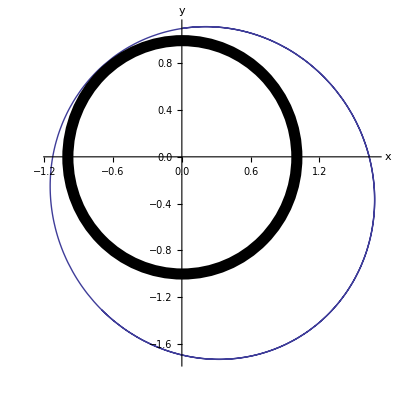

```mathematica
tm=3;P=4.0 π^2;
xinitial={0,6.6};yinitial={1.1,1};
eqs={x''[t]==-P*x[t]/((x[t]^2+y[t]^2)^(3/2)),
y''[t]==-P*y[t]/((x[t]^2+y[t]^2)^(3/2)),
x[0]==xinitial[[1]],x'[0]==xinitial[[2]],
y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
s=NDSolve[eqs,{x,y},{t,0,tm}];
{x,y}={x,y}/.s[[1]];
ParametricPlot[{x[t],y[t]},{t,0,tm},AxesLabel->{"x","y"},
Epilog->{Thickness[0.02],Circle[{0,0},1]}]
```

```mathematica
Clear[tm,P,xinitial,yinitial,eqs,x,y,s]
```

```mathematica
(*轨道参数的计算*)
```

Energy:-14.4445Angular Momentum7.15

Eccentricity:0.228914Half-long-axis1.36656

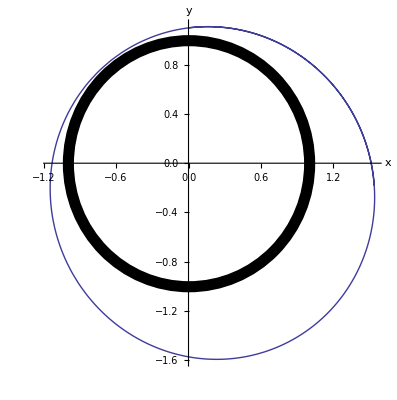

{1.67938,{t→0.68917}}

Apogee:1.06295,-1.30018

{1.05373,{t→1.48792}}

Perigee:-0.666952,0.8158

{t→0.231592}

a=1.36656,b=1.33027

```mathematica
tm=2.0;P=4.0 π^2;
xinitial={0,6.5};yinitial={1.1,0.8};
(*theoretically calculated parameters*)
energy=-P/(√(xinitial[[1]]^2+yinitial[[1]]^2))+1/2(xinitial[[2]]^2+yinitial[[2]]^2);
Angularmomentum=yinitial[[1]]*xinitial[[2]]-xinitial[[1]]*yinitial[[2]];
Print["Energy:",energy,"Angular Momentum",Abs[Angularmomentum]]
e=√(1+2/(2π)^4 energy*Angularmomentum^2);
a=-2 π^2/energy;
Print["Eccentricity:",e,"Half-long-axis",a]
(*solving orbit*)
eqs={x''[t]==-P*x[t]/((x[t]^2+y[t]^2)^(3/2)),
y''[t]==-P*y[t]/((x[t]^2+y[t]^2)^(3/2)),
x[0]==xinitial[[1]],x'[0]==xinitial[[2]],
y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
s=NDSolve[eqs,{x,y},{t,0,tm}];
{x,y}={x,y}/.s[[1]];
ParametricPlot[{x[t],y[t]},{t,0,tm},AxesLabel->{"x","y"},Epilog->{Thickness[0.02],Circle[{0,0},1]}]
(*Calculating parameters through orbit*)
r[t_]:=√(x[t]^2+y[t]^2);
apogee=FindMaximum[r[t],{t,0.5}]
{x1,y1}={x[t/.apogee[[2]]],y[t/.apogee[[2]]]};
Print["Apogee:",x1,",",y1]
perigee=FindMinimum[r[t],{t,1}]
{x2,y2}={x[t/.perigee[[2]]],y[t/.perigee[[2]]]};
Print["Perigee:",x2,",",y2]
a=(apogee[[1]]+perigee[[1]])/2;
slope[t_]:=y'[t]/x'[t];aslope=(y2-y1)/(x2-x1);
p=FindRoot[slope[t]==aslope,{t,0.25}]
{x3,y3}={x[t/.p],y[t/.p]};
b=√((y3-y1)^2+(x3-x1)^2-a^2);
Print["a=",a,",","b=",b]
```